```mathematica
Manipulate[ContourPlot[{B-x-x*y/(1+q*x^2)==0,A-x*y/(1+q*x^2)==0,x==B-A},{x,-10,3},{y,-10,3}],{A,0.1,10},{B,0.1,10},{q,0.1,10}]
```

```mathematica
Manipulate[Show[ContourPlot[{B-x-x*y/(1+q*x^2)==0,A-x*y/(1+q*x^2)==0,x==B-A},{x,-5,5},{y,-5,5}],StreamPlot[{B-x-x*y/(1+q*x^2),A-x*y/(1+q*x^2)},{x,-5,5},{y,-5,5},StreamStyle->Red]],{A,0.1,10},{B,0.1,10},{q,0.01,.2}]
```

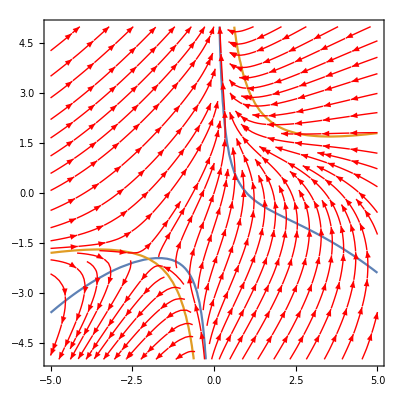

```mathematica
A1=3;B1=1;qq=0.08;Show[ContourPlot[{B1-x-x*y/(1+qq*x^2)==0,A1-x*y/(1+qq*x^2)==0},{x,-5,5},{y,-5,5}],StreamPlot[{B1-x-x*y/(1+qq*x^2),A1-x*y/(1+qq*x^2)},{x,-5,5},{y,-5,5},StreamStyle->Red]]
```

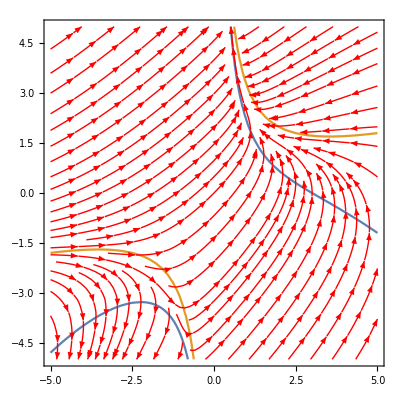

```mathematica
A1=3;B1=3;qq=0.08;Show[ContourPlot[{B1-x-x*y/(1+qq*x^2)==0,A1-x*y/(1+qq*x^2)==0},{x,-5,5},{y,-5,5}],StreamPlot[{B1-x-x*y/(1+qq*x^2),A1-x*y/(1+qq*x^2)},{x,-5,5},{y,-5,5},StreamStyle->Red]]
```

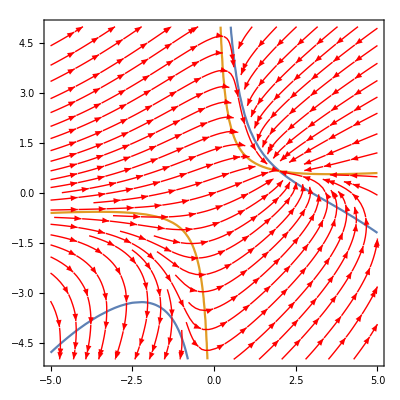

```mathematica
A1=1;B1=3;qq=0.08;Show[ContourPlot[{B1-x-x*y/(1+qq*x^2)==0,A1-x*y/(1+qq*x^2)==0},{x,-5,5},{y,-5,5}],StreamPlot[{B1-x-x*y/(1+qq*x^2),A1-x*y/(1+qq*x^2)},{x,-5,5},{y,-5,5},StreamStyle->Red]]
```

```mathematica
points = Join[Table[{x,(B1-x)(1+qq*x^2)/x},{x,-5.1,5.1,0.5}],Table[{x,A1(1+qq*x^2)/x},{x,-5.1,5.1,0.5}]];
```

```mathematica
xPrime[x_,y_]:=B1-x-x*y/(1+qq*x^2); yPrime[x_,y_]:=A1-x*y/(1+qq*x^2);
```

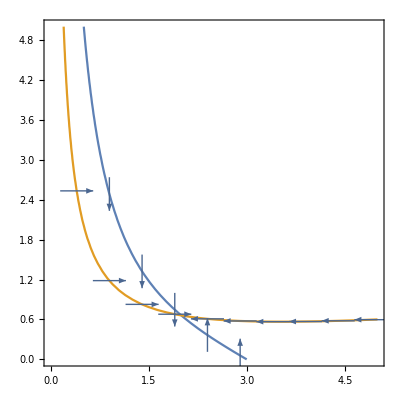

```mathematica
Show[ContourPlot[{B1-x-x*y/(1+qq*x^2)==0,A1-x*y/(1+qq*x^2)==0},{x,0,5},{y,0,5}],VectorPlot[{xPrime[x,y]/Sqrt[xPrime[x,y]^2+yPrime[x,y]^2],yPrime[x,y]/Sqrt[xPrime[x,y]^2+yPrime[x,y]^2]},{x,0,5},{y,0,5},VectorPoints->points]]
```

```mathematica
D[b-x-x*y/(1+q*x^2),x]
```

-1+(2 q x^2 y)/((1+q x^2)^2)-y/(1+q x^2)

```mathematica
D[b-x-x*y/(1+q*x^2),y]
```

-x/(1+q x^2)

```mathematica
D[a-x*y/(1+q*x^2),y]
```

-x/(1+q x^2)

```mathematica
Det[{{b-1,a},{-b,-a}}]
```

a